Define the functions to be used in the calculations.

```mathematica
vol[a_, b_, c_, d_, e_, f_]:= Sqrt[Det[{{0,1,1,1,1},{1, 0, a^2, b^2, c^2},{1, a^2,0, d^2,e^2 },{1, b^2, d^2, 0, f^2},{1,c^2,e^2,f^2, 0}}]/288];
A[x_, y_, z_]:= 1/4 Sqrt[(x+y+z)(x+y-z)(x-y+z)(y+z-x)];surf[a_, b_, c_, d_, e_, f_] := A[a, b, d]+A[b, c, f]+A[a, c, e]+A[d,e, f];
ratio[a_, b_, c_, d_, e_, f_]:= surf[a, b, c, d, e, f]/vol[a, b, c, d, e, f]^(2/3);
```

Calculation of Isoperimetric Tile from Goldberg Family 1:

```mathematica
ratio[1, Sqrt[1^2+3 a^2], 3 a, 1,  Sqrt[1^2+3 a^2],1]
```

(2 6^(2/3) (1/2 √((1+3 a^2) (2-√(1+3 a^2)) (2+√(1+3 a^2)))+1/2 √((1+3 a-√(1+3 a^2)) (1-3 a+√(1+3 a^2)) (-1+3 a+√(1+3 a^2)) (1+3 a+√(1+3 a^2)))))/(54 a^2-108 a^4+54 a^6)^(1/3)

```mathematica
Simplify[(2 6^(2/3) (1/2 √((1+3 a^2) (2-√(1+3 a^2)) (2+√(1+3 a^2)))+1/2 √((1+3 a-√(1+3 a^2)) (1-3 a+√(1+3 a^2)) (-1+3 a+√(1+3 a^2)) (1+3 a+√(1+3 a^2)))))/(54 a^2-108 a^4+54 a^6)^(1/3)]
```

((2/3)^(1/3) (√(3+6 a^2-9 a^4)+6 √(a^2-a^4)))/((a^2 (-1+a^2)^2)^(1/3))

```mathematica
FindMinimum[((2/3)^(1/3) (√(3+6 a^2-9 a^4)+6 √(a^2-a^4)))/((a^2 (-1+a^2)^2)^(1/3)), {a, 0.4}, PrecisionGoal->50]
```

{7.41258,{a→0.333333}}

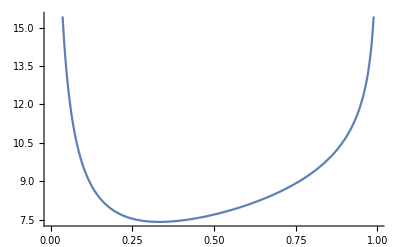

```mathematica
Plot[((2/3)^(1/3) (√(3+6 a^2-9 a^4)+6 √(a^2-a^4)))/((a^2 (-1+a^2)^2)^(1/3)), {a, 0, 1}]
```

Calculation of Alpha to specify the tetrahedron:

```mathematica
ArcSin[1/Sqrt[1+3 (0.33333333333354476)^2]]*180/Pi
```

60.

```mathematica
NumberForm[48.710619064264954,16]
```

48.71061906426496

Calculation for Isoperimetric Tile from Goldberg Family 2:

```mathematica
ratio[1, Sqrt[1^2+3 a^2], 3 a/2, 1, Sqrt[4-3a^2]/2, Sqrt[4-3a^2]/2]
```

1/(((27 a^2)/2-27 a^4+(27 a^6)/2)^(1/3))2 6^(2/3) (1/4 √((1+(3 a)/2-1/2 √(4-3 a^2)) (1-(3 a)/2+1/2 √(4-3 a^2)) (-1+(3 a)/2+1/2 √(4-3 a^2)) (1+(3 a)/2+1/2 √(4-3 a^2)))+1/4 √((-1+√(4-3 a^2)) (1+√(4-3 a^2)))+1/4 √((1+3 a^2) (2-√(1+3 a^2)) (2+√(1+3 a^2)))+1/4 √(((3 a)/2+1/2 √(4-3 a^2)-√(1+3 a^2)) ((3 a)/2-1/2 √(4-3 a^2)+√(1+3 a^2)) (-(3 a)/2+1/2 √(4-3 a^2)+√(1+3 a^2)) ((3 a)/2+1/2 √(4-3 a^2)+√(1+3 a^2))))

```mathematica
Simplify[%33]
```

```mathematica
(√(3-3 a^2)+√(3+6 a^2-9 a^4)+6 √(a^2-a^4))/(3^(1/3) (a^2 (-1+a^2)^2)^(1/3))
```

```mathematica
FindMinimum[(√(3-3 a^2)+√(3+6 a^2-9 a^4)+6 √(a^2-a^4))/(3^(1/3) (a^2 (-1+a^2)^2)^(1/3)), {a, 0.1}, PrecisionGoal->50]
```

{8.109,{a→0.490781}}

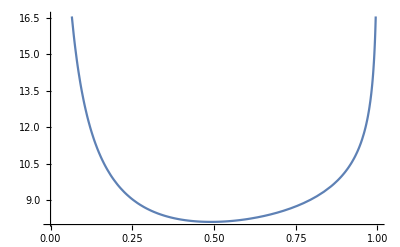

```mathematica
Plot[(√(3-3 a^2)+√(3+6 a^2-9 a^4)+6 √(a^2-a^4))/(3^(1/3) (a^2 (-1+a^2)^2)^(1/3)), {a, 0, 1}]
```

Calculation of Alpha and Beta to specify the tetrahedron:

```mathematica
ArcSin[1/Sqrt[1+3 (0.4907811558686964)^2]]*180/Pi
```

49.6335

Alpha:

```mathematica
NumberForm[49.633537633166476,16]
```

49.63353763316648

```mathematica
ArcSin[Sqrt[3 (0.4907811558686964)]/2]*180/Pi
```

37.3513

Beta:

```mathematica
NumberForm[37.35133009428851,16]
```

37.35133009428851

Calculation for Isoperimetric Tile from Goldberg Family 3:

```mathematica
ratio[1, Sqrt[1+2 (1+3a^2)]/2, 3a, 1/2, Sqrt[1+3a^2],  Sqrt[1+2 (1+3a^2)]/2]
```

1/(((27 a^2)/2-27 a^4+(27 a^6)/2)^(1/3))2 6^(2/3) (1/4 √((1+3 a-√(1+3 a^2)) (1-3 a+√(1+3 a^2)) (-1+3 a+√(1+3 a^2)) (1+3 a+√(1+3 a^2)))+1/4 √((3/2-1/2 √(1+2 (1+3 a^2))) (-1/2+1/2 √(1+2 (1+3 a^2))) (1/2+1/2 √(1+2 (1+3 a^2))) (3/2+1/2 √(1+2 (1+3 a^2))))+1/4 √((1/2+√(1+3 a^2)-1/2 √(1+2 (1+3 a^2))) (1/2-√(1+3 a^2)+1/2 √(1+2 (1+3 a^2))) (-1/2+√(1+3 a^2)+1/2 √(1+2 (1+3 a^2))) (1/2+√(1+3 a^2)+1/2 √(1+2 (1+3 a^2))))+3/4 √(a^2 (-3 a+√(1+2 (1+3 a^2))) (3 a+√(1+2 (1+3 a^2)))))

```mathematica
Simplify[%49]
```

(√(3+6 a^2-9 a^4)+6 √(a^2-a^4)+3 √3 √(a^2-a^4))/(3^(1/3) (a^2 (-1+a^2)^2)^(1/3))

```mathematica
FindMinimum[(√(3+6 a^2-9 a^4)+6 √(a^2-a^4)+3 √3 √(a^2-a^4))/(3^(1/3) (a^2 (-1+a^2)^2)^(1/3)), {a, 0.1}, PrecisionGoal->50]
```

{8.27318,{a→0.23764}}

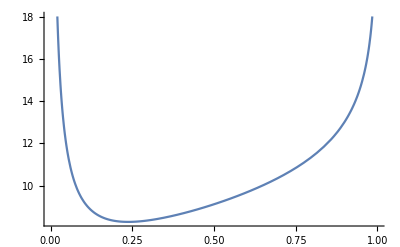

```mathematica
Plot[(√(3+6 a^2-9 a^4)+6 √(a^2-a^4)+3 √3 √(a^2-a^4))/(3^(1/3) (a^2 (-1+a^2)^2)^(1/3)), {a, 0, 1}]
```

Calculation of Alpha and Gamma to specify the tetrahedron:

```mathematica
ArcSin[1/Sqrt[1+3 (0.23763988950803772)^2]]*180/Pi
```

67.6277

Alpha:

```mathematica
NumberForm[67.62772054586142,16]
```

67.62772054586142

```mathematica
ArcSin[0.4828452798911604/Sqrt[1+3 (0.23763988950803772)^2]]*180/Pi
```

26.5195

Gamma:

```mathematica
NumberForm[26.51945444556687,16]
```

26.51945444556687